## Generate matches

From Reid C., Rosa A., “Steiner systems S(2, 4, v) — a survey,” Electronic Journal of Combinatorics (2010)

The system S(2,4, v) consists of a set V of v elements, and a set B of length-4 subsets of V such that that every length-2 subset of V appears in exactly one element of B.  In other words, V is a list of players, B is a list of four-player matches, and every player plays every other player at exactly once.  S(2, 4, v) is additionally called ‘resolvable’ if B can be partitioned so that each block of the partition is itself a partition of V.  In our case this corresponds to separating the matches into rounds so that each player is in exactly one match per round.

According to the reference cited above, (V, B) exists only when v ≡ 1 or 4 mod 12, and is resolvable only when v ≡ 0 mod 4.  This limits our choices to only v ≡ 4 mod 12: for example, 16, 28, and 40.
Examples of these Steiner systems were obtained from https://www.ccrwest.org/cover/steiner.html:

```mathematica
Needs["FiniteFields`"]
```

### Generation of S(2, 4, 28)

```mathematica
t=2;(*the case of v≡4 mod 12; this may not work for other values of t (≠2) since I haven't implemented the algorithm completely rigorously*)
v=12t+4;
pn=4t+1;(*p^n in the paper*)
ℱ=GF[pn];(*finite field of order p^n*)
X=Table[ReduceElement[FromElementCode[ℱ,i]],{i,0,pn-1}];(*elements in ℱ*)
Do[
If[Sort[Table[ReduceElement[a^n],{n,pn-1}]]==Sort[Rest[X]],
α=a;Break[]],
{a,X}];(*find a generator (a.k.a primitive root) α such that every nonzero element of ℱ is equal to α^i for some integer i*)
c=1;(*I guessed here, but it works.  I think any c such that α^c≠±1 will work, since then (α^c+1)/(α^c-1) is nonzero and there is no division by zero: therefore there exists some q such that (α^c+1)/(α^c-1)=α^q, by definition of α.  Since α cannot be 1 (1^i=1), then we just have to avoid -1, which should(?) be the last element considered, and there are usually (also ?) multiple generators*)
B=Flatten[Table[{
{{α^(2i)+j,1},{α^(2t+2i)+j,1},{α^(2i+c)+j,2},{α^(2t+2i+c)+j,2}},
{{α^(2i)+j,2},{α^(2t+2i)+j,2},{α^(2i+c)+j,3},{α^(2t+2i+c)+j,3}},
{{α^(2i)+j,3},{α^(2t+2i)+j,3},{α^(2i+c)+j,1},{α^(2t+2i+c)+j,1}},
{{∞},{j,1},{j,2},{j,3}}
},{i,0,t-1},{j,X}],2];(*find the base blocks and all of the cyclical permutations at the same time.  Note that ∞ is a fixed point*)
B=B/.{e:(_GF[___]):>ToElementCode[e]};(*convert field elements to numbers so that Union[] works later*)
V=Union[Flatten[B,1]];
B=B/.Thread[V->Range[v]];(*convert the elements of V to numbers for easy processing later*)
V=Range[v];
B=Union[Sort/@B](*eliminate duplicates*)
```

{{1,2,3,4},{1,5,6,7},{1,8,9,10},{1,11,12,13},{1,14,15,16},{1,17,18,19},{1,20,21,22},{1,23,24,25},{1,26,27,28},{2,5,18,27},{2,6,21,23},{2,7,13,14},{2,8,15,24},{2,9,12,17},{2,10,22,26},{2,11,25,28},{2,16,19,20},{3,5,11,15},{3,6,19,28},{3,7,22,24},{3,8,20,27},{3,9,16,25},{3,10,13,18},{3,12,23,26},{3,14,17,21},{4,5,20,25},{4,6,12,16},{4,7,17,26},{4,8,11,19},{4,9,21,28},{4,10,14,23},{4,13,24,27},{4,15,18,22},{5,8,12,21},{5,9,24,26},{5,10,16,17},{5,13,19,23},{5,14,22,28},{6,8,14,18},{6,9,13,22},{6,10,25,27},{6,11,17,24},{6,15,20,26},{7,8,23,28},{7,9,15,19},{7,10,11,20},{7,12,18,25},{7,16,21,27},{8,13,16,26},{8,17,22,25},{9,11,14,27},{9,18,20,23},{10,12,15,28},{10,19,21,24},{11,16,22,23},{11,18,21,26},{12,14,20,24},{12,19,22,27},{13,15,21,25},{13,17,20,28},{14,19,25,26},{15,17,23,27},{16,18,24,28}}

### Pregenerated systems

```mathematica
B15={{2,3,7,9},{6,7,8,10},{1,7,15,16},{1,3,12,14},{1,2,6,13},{1,9,10,11},{2,4,10,12},{1,4,5,8},{10,13,14,16},{8,9,12,16},{3,8,11,13},{2,5,11,16},{5,7,12,13},{3,4,6,16},{5,6,9,14},{2,8,14,15},{4,9,13,15},{6,11,12,15},{4,7,11,14},{3,5,10,15}};
B28={{1,8,15,22},{2,9,16,23},{3,10,17,24},{4,11,18,25},{5,12,19,26},{6,13,20,27},{7,14,21,28},{2,4,12,13},{3,5,13,14},{4,6,8,14},{5,7,8,9},{1,6,9,10},{2,7,10,11},{1,3,11,12},{9,11,19,20},{10,12,20,21},{11,13,15,21},{12,14,15,16},{8,13,16,17},{9,14,17,18},{8,10,18,19},{17,21,23,25},{15,18,24,26},{16,19,25,27},{17,20,26,28},{18,21,22,27},{15,19,23,28},{16,20,22,24},{5,6,24,28},{6,7,22,25},{1,7,23,26},{1,2,24,27},{2,3,25,28},{3,4,22,26},{4,5,23,27},{3,7,16,18},{1,4,17,19},{2,5,18,20},{3,6,19,21},{4,7,15,20},{1,5,16,21},{2,6,15,17},{10,14,26,27},{8,11,27,28},{9,12,22,28},{10,13,22,23},{11,14,23,24},{8,12,24,25},{9,13,25,26},{1,14,20,25},{2,8,21,26},{3,9,15,27},{4,10,16,28},{5,11,17,22},{6,12,18,23},{7,13,19,24},{1,13,18,28},{2,14,19,22},{3,8,20,23},{4,9,21,24},{5,10,15,25},{6,11,16,26},{7,12,17,27}};
B40={{1,2,7,32},{1,3,13,24},{1,4,8,23},{1,5,20,37},{1,6,31,39},{1,9,10,15},{1,11,22,38},{1,12,28,30},{1,14,27,40},{1,16,33,36},{1,17,19,29},{1,18,21,25},{1,26,34,35},{2,3,8,33},{2,4,14,25},{2,5,9,24},{2,6,21,38},{2,10,11,16},{2,12,23,39},{2,13,29,31},{2,15,28,40},{2,17,34,37},{2,18,20,30},{2,19,22,26},{2,27,35,36},{3,4,9,34},{3,5,15,26},{3,6,10,25},{3,7,22,39},{3,11,12,17},{3,14,30,32},{3,16,29,40},{3,18,35,38},{3,19,21,31},{3,20,23,27},{3,28,36,37},{4,5,10,35},{4,6,16,27},{4,7,11,26},{4,12,13,18},{4,15,31,33},{4,17,30,40},{4,19,36,39},{4,20,22,32},{4,21,24,28},{4,29,37,38},{5,6,11,36},{5,7,17,28},{5,8,12,27},{5,13,14,19},{5,16,32,34},{5,18,31,40},{5,21,23,33},{5,22,25,29},{5,30,38,39},{6,7,12,37},{6,8,18,29},{6,9,13,28},{6,14,15,20},{6,17,33,35},{6,19,32,40},{6,22,24,34},{6,23,26,30},{7,8,13,38},{7,9,19,30},{7,10,14,29},{7,15,16,21},{7,18,34,36},{7,20,33,40},{7,23,25,35},{7,24,27,31},{8,9,14,39},{8,10,20,31},{8,11,15,30},{8,16,17,22},{8,19,35,37},{8,21,34,40},{8,24,26,36},{8,25,28,32},{9,11,21,32},{9,12,16,31},{9,17,18,23},{9,20,36,38},{9,22,35,40},{9,25,27,37},{9,26,29,33},{10,12,22,33},{10,13,17,32},{10,18,19,24},{10,21,37,39},{10,23,36,40},{10,26,28,38},{10,27,30,34},{11,13,23,34},{11,14,18,33},{11,19,20,25},{11,24,37,40},{11,27,29,39},{11,28,31,35},{12,14,24,35},{12,15,19,34},{12,20,21,26},{12,25,38,40},{12,29,32,36},{13,15,25,36},{13,16,20,35},{13,21,22,27},{13,26,39,40},{13,30,33,37},{14,16,26,37},{14,17,21,36},{14,22,23,28},{14,31,34,38},{15,17,27,38},{15,18,22,37},{15,23,24,29},{15,32,35,39},{16,18,28,39},{16,19,23,38},{16,24,25,30},{17,20,24,39},{17,25,26,31},{18,26,27,32},{19,27,28,33},{20,28,29,34},{21,29,30,35},{22,30,31,36},{23,31,32,37},{24,32,33,38},{25,33,34,39}};
```

```mathematica
B=B40;
V=Union[Flatten[B]];
v=Length[V];
```

```mathematica
B
```

{{1,2,7,32},{1,3,13,24},{1,4,8,23},{1,5,20,37},{1,6,31,39},{1,9,10,15},{1,11,22,38},{1,12,28,30},{1,14,27,40},{1,16,33,36},{1,17,19,29},{1,18,21,25},{1,26,34,35},{2,3,8,33},{2,4,14,25},{2,5,9,24},{2,6,21,38},{2,10,11,16},{2,12,23,39},{2,13,29,31},{2,15,28,40},{2,17,34,37},{2,18,20,30},{2,19,22,26},{2,27,35,36},{3,4,9,34},{3,5,15,26},{3,6,10,25},{3,7,22,39},{3,11,12,17},{3,14,30,32},{3,16,29,40},{3,18,35,38},{3,19,21,31},{3,20,23,27},{3,28,36,37},{4,5,10,35},{4,6,16,27},{4,7,11,26},{4,12,13,18},{4,15,31,33},{4,17,30,40},{4,19,36,39},{4,20,22,32},{4,21,24,28},{4,29,37,38},{5,6,11,36},{5,7,17,28},{5,8,12,27},{5,13,14,19},{5,16,32,34},{5,18,31,40},{5,21,23,33},{5,22,25,29},{5,30,38,39},{6,7,12,37},{6,8,18,29},{6,9,13,28},{6,14,15,20},{6,17,33,35},{6,19,32,40},{6,22,24,34},{6,23,26,30},{7,8,13,38},{7,9,19,30},{7,10,14,29},{7,15,16,21},{7,18,34,36},{7,20,33,40},{7,23,25,35},{7,24,27,31},{8,9,14,39},{8,10,20,31},{8,11,15,30},{8,16,17,22},{8,19,35,37},{8,21,34,40},{8,24,26,36},{8,25,28,32},{9,11,21,32},{9,12,16,31},{9,17,18,23},{9,20,36,38},{9,22,35,40},{9,25,27,37},{9,26,29,33},{10,12,22,33},{10,13,17,32},{10,18,19,24},{10,21,37,39},{10,23,36,40},{10,26,28,38},{10,27,30,34},{11,13,23,34},{11,14,18,33},{11,19,20,25},{11,24,37,40},{11,27,29,39},{11,28,31,35},{12,14,24,35},{12,15,19,34},{12,20,21,26},{12,25,38,40},{12,29,32,36},{13,15,25,36},{13,16,20,35},{13,21,22,27},{13,26,39,40},{13,30,33,37},{14,16,26,37},{14,17,21,36},{14,22,23,28},{14,31,34,38},{15,17,27,38},{15,18,22,37},{15,23,24,29},{15,32,35,39},{16,18,28,39},{16,19,23,38},{16,24,25,30},{17,20,24,39},{17,25,26,31},{18,26,27,32},{19,27,28,33},{20,28,29,34},{21,29,30,35},{22,30,31,36},{23,31,32,37},{24,32,33,38},{25,33,34,39}}

## Split matches into rounds

Partition the set of matches so that each block (round) contains every player once.

```mathematica
f[list_,remaining_]:=If[(*yay, a recursive algorithm!*)
remaining=={},(*base case, if there are not more blocks remaining, return the completed list*)
list,
Block[{return=None,next=First[remaining],rest=Rest[remaining]},
current=list;
Do[(*loop over each subset*)
If[Intersection[Flatten[list[[i]]],next]=={},(*if none of the elements in the block are in the given subset already*)
return=f[MapAt[Append[#,next]&,list,i],rest];(*recurse, adding the next block to the given subset*)
If[return===None,(*if return = None, the rest of the blocks didn't 'fit,' continue and try the next subset*)
,
Break[];
]
],
{i,Length[list]}];
return](*if return ≠ None, the base case has been reached: pass it to the previous recursive level; otherwise let that level know you've exhausted all the possible arrangements)
]
Dynamic[Grid@current]
sets=f[ConstantArray[{},4Length[B]/v],B](*initialize each of the rounds to be empty*)
```

```mathematica
Partition
```

```mathematica
Last/@(Tally@(Sort/@Flatten[Subsets[#,{2}]&/@B,1]))
```

{4,3,3,4,3,3,4,2,2,2,2,4,2,2,2,2,4,3,3,2,2,2,4,2,2,2,2,4,2,2,4,4,2,2,2,2,2,4,4,2,2,2,2,4,3,2,2,4,3,2,2,2,4,2,2,4,2,2,2,4,4,2,3,2,2,2,2,2,2,4,2,2,4,4,2,2,3,2,2,2,4,2,2,2,2,2,2,2,2,4,2,2,2,2,4,4,2,2,2,2,2,3,2,2,2,4,2,4,3,3,4,3,4,2,2,2,2,4,2,2,2,2,2,2,2,4,2,2,2,2,4,2,2,4,4,2,2,2,2,2,2,2,4,3,2,2,4,3,2,2,2,4,2,2,4,2,2,2,4,4,2,2,2,2,2,2,2,4,2,2,4,4,2,3,2,2,2,2,2,2,2,2,2,4,2,2,2,2,4,4,2,2,2,2,3,2,2,3,4,3,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,4,2,2,4,4,2,2,2,2,2,2,2,4,3,2,2,4,3,2,2,2,4,2,2,4,2,2,4,2,2,2,2,4,2,2,4,4,2,3,2,2,2,2,2,2,2,2,2,4,2,2,2,4,2,3,2,2,3,4,3,2,2,2,2,2,2,2,4,2,2,4,2,2,2,2,2,2,2,2,4,3,2,4,3,2,2,2,4,2,2,4,2,2,4,2,2,4,2,3,2,2,2,2,2,2,4,2,2,4,3,2,3,4,3,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,3,2,4,3,2,2,2,4,2,2,4,2,2,4,2,2,4,2,2,2,2,2,4,2,2,4,3,3,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,3,2,3,2,2,2,4,2,2,4,2,2,4,2,2,2,2,4,2,2,3,3,2,2,2,4,2,2,2,2,2,2,2,2,3,2,2,2,4,4,2,2,4,2,2,2,2,2,3,3,2,2,2,4,2,2,2,2,2,2,3,2,2,2,4,4,2,2,4,2,2,2,2,2,3,3,2,2,2,4,2,2,2,2,2,2,3,2,2,2,4,2,2,4,2,2,2,3,2,2,2,4,2,2,2,2,3,2,2,4,2,2,4,2,2,2,3,2,2,2,4,2,2,2,3,2,2,4,2,2,4,2,2,2,3,2,2,2,4,2,2,2,3,2,2,4,2,2,4,2,2,3,2,2,2,4,2,2,2,3,2,2,4,2,2,4,2,2,3,2,2,2,4,2,2,2,3,2,2,2,4,2,2,3,2,2,2,4,2,2,2,2,2,2,4,2,3,2,2,2,4,2,2,2,2,2,2,4,3,2,2,2,2,2,2,2,2,4,3,2,2,2,2,2,2,2,3,2,2,2,2,3,2,2,2,2,3,2,2,2,2,3,2,2,2,3,2,2,2,3,2,2,2,3,2,3,2,3,2,3,3,3,3,3,3,3,3}

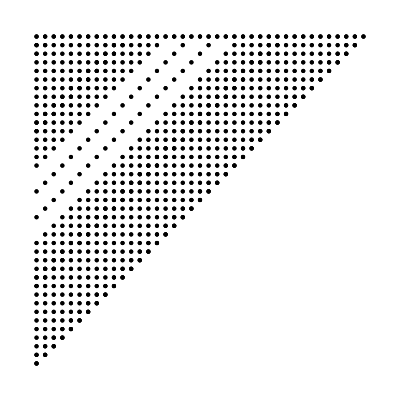

```mathematica
Graphics[Point[Flatten[Subsets[#,{2}]&/@B,1]]]
```

## Order matches/rounds

```mathematica
g[list_,remaining_,n_]:=If[
remaining=={},
list,
Block[{return=None},
Do[(*loop over each match in the current round*)
If[Intersection[Flatten[list[[-n;;]]],choice]=={},(*any of the teams in the selected match have not participated in the last n matches...*)
return=g[(*recurse!*)
Append[list,choice],(*add the current match to the sequence*)
If[
Length[First[remaining]]==1,(*if there is only one match remaining in the current round...*)
Rest[remaining],(*return all of the following rounds*)
Prepend[Rest[remaining],DeleteCases[First[remaining],choice]](*otherwise, delete the selected match from the round*)
],
n];
If[return===None,
,
Break[];(*if return ≠ None, break the loop and return*)
]
],
{choice,First[remaining]}];
return](*the structure is pretty much the same as the previous recursive function*)
]
best={};(*initialize the counter*)
Dynamic[best]
n=0;
Do[(*for every ordering (permutation) of the rounds:*)
While[True,
current=g[First[s],Rest[s],n];(*calculate an ordering with the previous best spacing+1*)
If[current===None,(*if it failed...*)
Break[],(*break out of the while-loop, continue to the next permutation*)
best=current(*otherwise we have a new best ordering*)
];
n++(*increase the spacing by one for the next ordering*)
],
{s,Permutations[sets]}];(*I don't know if the loop actually helps, but it only takes like 30 seconds*)
ordering=best/.Thread[Take[Flatten[best],v]->V];(*use an isomporphism to map the result onto itself with a specified ordering*)
```

## Visualization

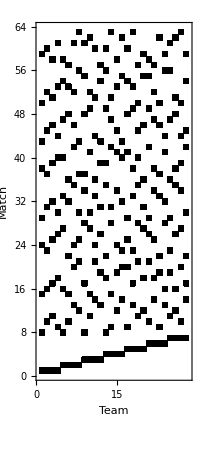

Round 1, match 1: Teams  1,  2,  3, and  4
Round 1, match 2: Teams  5,  6,  7, and  8
Round 1, match 3: Teams  9, 10, 11, and 12
Round 1, match 4: Teams 13, 14, 15, and 16
Round 1, match 5: Teams 17, 18, 19, and 20
Round 1, match 6: Teams 21, 22, 23, and 24
Round 1, match 7: Teams 25, 26, 27, and 28
Round 2, match 1: Teams  1,  5,  9, and 13
Round 2, match 2: Teams  4, 14, 17, and 23
Round 2, match 3: Teams  2,  6, 21, and 27
Round 2, match 4: Teams  3, 10, 25, and 19
Round 2, match 5: Teams 15, 26,  8, and 20
Round 2, match 6: Teams  7, 18, 12, and 24
Round 2, match 7: Teams 11, 22, 16, and 28
Round 3, match 1: Teams  1,  6, 10, and 14
Round 3, match 2: Teams  2,  5, 26, and 24
Round 3, match 3: Teams  3,  9, 18, and 28
Round 3, match 4: Teams  4, 13, 22, and 20
Round 3, match 5: Teams 15, 25, 12, and 23
Round 3, match 6: Teams  7, 17, 16, and 27
Round 3, match 7: Teams 11, 21,  8, and 19
Round 4, match 1: Teams 13,  6, 23, and 28
Round 4, match 2: Teams  2, 25, 18, and 16
Round 4, match 3: Teams  1, 15,  7, and 11
Round 4, match 4: Teams  3, 17, 22, and  8
Round 4, match 5: Teams  4, 21, 26, and 12
Round 4, match 6: Teams  5, 10, 27, and 20
Round 4, match 7: Teams  9, 14, 19, and 24
Round 5, match 1: Teams  1, 17, 21, and 25
Round 5, match 2: Teams  4, 10,  8, and 28
Round 5, match 3: Teams  2, 14, 12, and 20
Round 5, match 4: Teams  3,  6, 16, and 24
Round 5, match 5: Teams  5, 11, 18, and 23
Round 5, match 6: Teams  9, 15, 22, and 27
Round 5, match 7: Teams 13,  7, 26, and 19
Round 6, match 1: Teams  6, 11, 25, and 20
Round 6, match 2: Teams  2,  9,  8, and 23
Round 6, match 3: Teams  1, 22, 26, and 18
Round 6, match 4: Teams  3, 13, 12, and 27
Round 6, match 5: Teams  4,  5, 16, and 19
Round 6, match 6: Teams 10, 15, 17, and 24
Round 6, match 7: Teams 14,  7, 21, and 28
Round 7, match 1: Teams  1, 16,  8, and 12
Round 7, match 2: Teams  4, 11, 27, and 24
Round 7, match 3: Teams  2, 15, 19, and 28
Round 7, match 4: Teams  3,  7, 23, and 20
Round 7, match 5: Teams  5, 14, 25, and 22
Round 7, match 6: Teams  9,  6, 17, and 26
Round 7, match 7: Teams 13, 10, 21, and 18
Round 8, match 1: Teams  1, 23, 27, and 19
Round 8, match 2: Teams  3, 14, 11, and 26
Round 8, match 3: Teams  2, 10,  7, and 22
Round 8, match 4: Teams  4,  6, 15, and 18
Round 8, match 5: Teams  5, 17, 12, and 28
Round 8, match 6: Teams  9, 21, 16, and 20
Round 8, match 7: Teams 13, 25,  8, and 24
Round 9, match 1: Teams  6, 22, 12, and 19
Round 9, match 2: Teams  3,  5, 15, and 21
Round 9, match 3: Teams  1, 20, 24, and 28
Round 9, match 4: Teams  2, 13, 11, and 17
Round 9, match 5: Teams  4,  9,  7, and 25
Round 9, match 6: Teams 10, 26, 16, and 23
Round 9, match 7: Teams 14, 18,  8, and 27

Team  1: matches 1, 1, 1, 3, 1, 3, 1, 1, and 3
Team  2: matches 1, 3, 2, 2, 3, 2, 3, 3, and 4
Team  3: matches 1, 4, 3, 4, 4, 4, 4, 2, and 2
Team  4: matches 1, 2, 4, 5, 2, 5, 2, 4, and 5
Team  5: matches 2, 1, 2, 6, 5, 5, 5, 5, and 2
Team  6: matches 2, 3, 1, 1, 4, 1, 6, 4, and 1
Team  7: matches 2, 6, 6, 3, 7, 7, 4, 3, and 5
Team  8: matches 2, 5, 7, 4, 2, 2, 1, 7, and 7
Team  9: matches 3, 1, 3, 7, 6, 2, 6, 6, and 5
Team 10: matches 3, 4, 1, 6, 2, 6, 7, 3, and 6
Team 11: matches 3, 7, 7, 3, 5, 1, 2, 2, and 4
Team 12: matches 3, 6, 5, 5, 3, 4, 1, 5, and 1
Team 13: matches 4, 1, 4, 1, 7, 4, 7, 7, and 4
Team 14: matches 4, 2, 1, 7, 3, 7, 5, 2, and 7
Team 15: matches 4, 5, 5, 3, 6, 6, 3, 4, and 2
Team 16: matches 4, 7, 6, 2, 4, 5, 1, 6, and 6
Team 17: matches 5, 2, 6, 4, 1, 6, 6, 5, and 4
Team 18: matches 5, 6, 3, 2, 5, 3, 7, 4, and 7
Team 19: matches 5, 4, 7, 7, 7, 5, 3, 1, and 1
Team 20: matches 5, 5, 4, 6, 3, 1, 4, 6, and 3
Team 21: matches 6, 3, 7, 5, 1, 7, 7, 6, and 2
Team 22: matches 6, 7, 4, 4, 6, 3, 5, 3, and 1
Team 23: matches 6, 2, 5, 1, 5, 2, 4, 1, and 6
Team 24: matches 6, 6, 2, 7, 4, 6, 2, 7, and 3
Team 25: matches 7, 4, 5, 2, 1, 1, 5, 7, and 5
Team 26: matches 7, 5, 2, 5, 7, 3, 6, 2, and 6
Team 27: matches 7, 3, 6, 6, 6, 4, 2, 1, and 7
Team 28: matches 7, 7, 3, 1, 2, 7, 3, 5, and 3

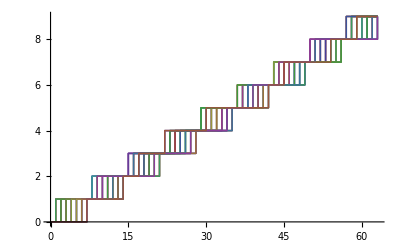

```mathematica
positions=(Flatten/@Flatten[MapIndexed[List,ordering,{2}],1])[[;;,;;2]];
(*draw a sort of schedule diagram thingey*)
Graphics[Rectangle/@(positions-1/2),GridLines->{Range,Range},PlotRange->{{0,28}+1/2,{0,63}+1/2},Frame->True,FrameLabel->{"Team","Match"}]
(*schedule: which teams play in a given match*)
Column[MapIndexed[Row[Flatten[{"Round ",Ceiling[First[#2]/7],", match ",Mod[First[#2],7,1],": Teams ",Insert[Riffle[PaddedForm[#,2,NumberSigns->{"",""}]&/@#1,", "],"and ",-2]}]]&,ordering]]
(*itinerary: which matches a given team plays*)
Column[MapIndexed[Row[Flatten[{"Team ",PaddedForm[First[#2],2,NumberSigns->{"",""}],": matches ",Insert[Riffle[{Mod[#,7,1]}&/@#1,", "],"and ",-2]}]]&,SplitBy[Sort[positions],First][[;;,;;,2]]]]
(*graph the number of matches per team over time; shows that no team has more than one more match played than any other team*)
ListLinePlot[Transpose[{Flatten@Partition[Prepend[Append[Last/@#,Length[ordering]],0],2,1],Floor@Range[0,Length[#]+1/2,1/2]}]&/@SplitBy[Sort[positions],First]]
```

```mathematica
Binomial[29,4]
```

23751

```mathematica
Binomial[28,3]Binomial[24,3]Binomial[20,3]Binomial[16,3]Binomial[12,3]Binomial[8,3]Binomial[4,3]Binomial[1,1]
```

```mathematica
208601765019648000
```

```mathematica
208601765019648000/382498372653271875
```

262144/480675

```mathematica
v=28;
V=Range[v];
k=4;
(Binomial[v,2]/6)/(v/4)
h[previous_,pairs_,current_,remaining_]:=If[remaining==0||Length[pairs]==Binomial[v,2],
previous,
Block[{pts=Complement[V,Flatten[current]],return=None},
If[Length[pts]>k,
Do[
return=h[previous,pairs,Append[current,subset],remaining];
If[Length[return]>0,Break[]],
{subset,Select[Prepend[#,First[pts]]&/@Subsets[Complement[Rest[pts],Cases[pairs,{First[pts],s_}:>s]],{k-1}],Intersection[Subsets[#,{2}],pairs]=={}&]}
];
return,
If[Intersection[Subsets[pts,{2}],pairs]=={},
Block[{next=Append[current,pts]},
h[c=Append[previous,next],Join[pairs,Flatten[Subsets[#,{2}]&/@next,1]],{},remaining-1]
],
None]
]
]
]
Dynamic[Grid@c]
Timing[rounds=h[{},{},{},∞];]
```

9

$Aborted

```mathematica
Divisors[163]
```

{1,163}

```mathematica
rounds
```

{{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16},{17,18,19,20},{21,22,23,24},{25,26,27,28},{29}},{{1,5,9,13},{2,6,10,14},{3,7,11,15},{4,8,17,21},{12,18,22,25},{16,19,23,26},{20,24,27,29},{28}},{{1,6,11,16},{2,5,12,15},{3,8,9,14},{4,7,18,23},{10,17,24,25},{13,20,21,26},{19,22,28,29},{27}},{{1,7,10,19},{2,8,11,13},{3,5,16,17},{4,6,9,22},{12,20,23,28},{14,18,24,26},{15,21,25,29},{27}},{{1,8,12,24},{2,7,9,16},{3,6,13,25},{4,14,19,27},{5,18,21,28},{10,15,20,22},{11,17,23,29},{26}},{{1,14,23,25},{2,17,22,26},{3,12,19,21},{4,5,11,20},{6,15,18,27},{7,13,24,28},{8,10,16,29},{9}}}

```mathematica
Subsets[V,{Length[V]}]
```

```mathematica
.
```

{{1,2,3,4,5,6,7,8,9}}

```mathematica
Solve[2n1 Log2[n1]==n2 Normal[Series[Log2[n2],{n2,n1,1}]],n2]//Simplify
```

```mathematica
Grid[{Divisors[360],
360/Divisors[360]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 8 | 9 | 10 | 12 | 15 | 18 | 20 | 24 | 30 | 36 | 40 | 45 | 60 | 72 | 90 | 120 | 180 | 360
360 | 180 | 120 | 90 | 72 | 60 | 45 | 40 | 36 | 30 | 24 | 20 | 18 | 15 | 12 | 10 | 9 | 8 | 6 | 5 | 4 | 3 | 2 | 1

```mathematica
B28={{1,8,15,22},{2,9,16,23},{3,10,17,24},{4,11,18,25},{5,12,19,26},{6,13,20,27},{7,14,21,28},{2,4,12,13},{3,5,13,14},{4,6,8,14},{5,7,8,9},{1,6,9,10},{2,7,10,11},{1,3,11,12},{9,11,19,20},{10,12,20,21},{11,13,15,21},{12,14,15,16},{8,13,16,17},{9,14,17,18},{8,10,18,19},{17,21,23,25},{15,18,24,26},{16,19,25,27},{17,20,26,28},{18,21,22,27},{15,19,23,28},{16,20,22,24},{5,6,24,28},{6,7,22,25},{1,7,23,26},{1,2,24,27},{2,3,25,28},{3,4,22,26},{4,5,23,27},{3,7,16,18},{1,4,17,19},{2,5,18,20},{3,6,19,21},{4,7,15,20},{1,5,16,21},{2,6,15,17},{10,14,26,27},{8,11,27,28},{9,12,22,28},{10,13,22,23},{11,14,23,24},{8,12,24,25},{9,13,25,26},{1,14,20,25},{2,8,21,26},{3,9,15,27},{4,10,16,28},{5,11,17,22},{6,12,18,23},{7,13,19,24},{1,13,18,28},{2,14,19,22},{3,8,20,23},{4,9,21,24},{5,10,15,25},{6,11,16,26},{7,12,17,27}};
```

```mathematica
Table[Tally@Flatten[Function[l,Length/@Split[Sort[Flatten[l]]]]/@Partition[B28,i,1]],{i,2,4}]
```

{{{1,440},{2,28}},{{1,558},{2,84},{3,2}},{{1,627},{2,150},{3,11}}}

```mathematica
bs=Table[RandomSample[B28],{j,200000}];
```

```mathematica
goodness=Table[Length[Flatten[Intersection@@@Partition[Take[b,20],2,1]]],{b,bs}];
```

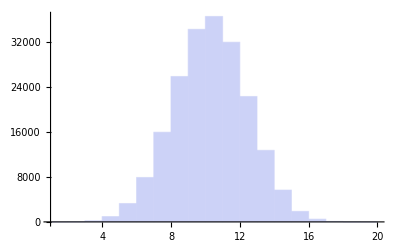

```mathematica
Histogram[goodness]
```

```mathematica
Min[goodness]
```

1

```mathematica
Take[Extract[bs,Ordering[goodness,1]],30]
```

{{4,11,18,25},{10,13,22,23},{6,7,22,25},{3,9,15,27},{5,6,24,28},{1,4,17,19},{2,9,16,23},{1,13,18,28},{10,14,26,27},{5,11,17,22},{4,7,15,20},{8,11,27,28},{3,5,13,14},{1,8,15,22},{2,4,12,13},{9,11,19,20},{2,3,25,28},{12,14,15,16},{1,2,24,27},{10,12,20,21},{5,7,8,9},{2,8,21,26},{8,12,24,25},{1,6,9,10},{5,10,15,25},{9,12,22,28},{4,5,23,27},{2,6,15,17},{6,13,20,27},{3,4,22,26}}

```mathematica
B28
```

{{1,8,15,22},{2,9,16,23},{3,10,17,24},{4,11,18,25},{5,12,19,26},{6,13,20,27},{7,14,21,28},{2,4,12,13},{3,5,13,14},{4,6,8,14},{5,7,8,9},{1,6,9,10},{2,7,10,11},{1,3,11,12},{9,11,19,20},{10,12,20,21},{11,13,15,21},{12,14,15,16},{8,13,16,17},{9,14,17,18},{8,10,18,19},{17,21,23,25},{15,18,24,26},{16,19,25,27},{17,20,26,28},{18,21,22,27},{15,19,23,28},{16,20,22,24},{5,6,24,28},{6,7,22,25},{1,7,23,26},{1,2,24,27},{2,3,25,28},{3,4,22,26},{4,5,23,27},{3,7,16,18},{1,4,17,19},{2,5,18,20},{3,6,19,21},{4,7,15,20},{1,5,16,21},{2,6,15,17},{10,14,26,27},{8,11,27,28},{9,12,22,28},{10,13,22,23},{11,14,23,24},{8,12,24,25},{9,13,25,26},{1,14,20,25},{2,8,21,26},{3,9,15,27},{4,10,16,28},{5,11,17,22},{6,12,18,23},{7,13,19,24},{1,13,18,28},{2,14,19,22},{3,8,20,23},{4,9,21,24},{5,10,15,25},{6,11,16,26},{7,12,17,27}}

```mathematica
data={{"Round "1", match "1": Teams "" 1"", "" 2"", "" 3"", ""and "" 4"}, {"Round "1", match "2": Teams "" 5"", "" 6"", "" 7"", ""and "" 8"}, {"Round "1", match "3": Teams "" 9"", ""10"", ""11"", ""and ""12"}, {"Round "1", match "4": Teams ""13"", ""14"", ""15"", ""and ""16"}, {"Round "1", match "5": Teams ""17"", ""18"", ""19"", ""and ""20"}, {"Round "1", match "6": Teams ""21"", ""22"", ""23"", ""and ""24"}, {"Round "1", match "7": Teams ""25"", ""26"", ""27"", ""and ""28"}, {"Round "2", match "1": Teams "" 1"", "" 5"", "" 9"", ""and ""13"}, {"Round "2", match "2": Teams "" 4"", ""14"", ""17"", ""and ""23"}, {"Round "2", match "3": Teams "" 2"", "" 6"", ""21"", ""and ""27"}, {"Round "2", match "4": Teams "" 3"", ""10"", ""25"", ""and ""19"}, {"Round "2", match "5": Teams ""15"", ""26"", "" 8"", ""and ""20"}, {"Round "2", match "6": Teams "" 7"", ""18"", ""12"", ""and ""24"}, {"Round "2", match "7": Teams ""11"", ""22"", ""16"", ""and ""28"}, {"Round "3", match "1": Teams "" 1"", "" 6"", ""10"", ""and ""14"}, {"Round "3", match "2": Teams "" 2"", "" 5"", ""26"", ""and ""24"}, {"Round "3", match "3": Teams "" 3"", "" 9"", ""18"", ""and ""28"}, {"Round "3", match "4": Teams "" 4"", ""13"", ""22"", ""and ""20"}, {"Round "3", match "5": Teams ""15"", ""25"", ""12"", ""and ""23"}, {"Round "3", match "6": Teams "" 7"", ""17"", ""16"", ""and ""27"}, {"Round "3", match "7": Teams ""11"", ""21"", "" 8"", ""and ""19"}, {"Round "4", match "1": Teams ""13"", "" 6"", ""23"", ""and ""28"}, {"Round "4", match "2": Teams "" 2"", ""25"", ""18"", ""and ""16"}, {"Round "4", match "3": Teams "" 1"", ""15"", "" 7"", ""and ""11"}, {"Round "4", match "4": Teams "" 3"", ""17"", ""22"", ""and "" 8"}, {"Round "4", match "5": Teams "" 4"", ""21"", ""26"", ""and ""12"}, {"Round "4", match "6": Teams "" 5"", ""10"", ""27"", ""and ""20"}, {"Round "4", match "7": Teams "" 9"", ""14"", ""19"", ""and ""24"}, {"Round "5", match "1": Teams "" 1"", ""17"", ""21"", ""and ""25"}, {"Round "5", match "2": Teams "" 4"", ""10"", "" 8"", ""and ""28"}, {"Round "5", match "3": Teams "" 2"", ""14"", ""12"", ""and ""20"}, {"Round "5", match "4": Teams "" 3"", "" 6"", ""16"", ""and ""24"}, {"Round "5", match "5": Teams "" 5"", ""11"", ""18"", ""and ""23"}, {"Round "5", match "6": Teams "" 9"", ""15"", ""22"", ""and ""27"}, {"Round "5", match "7": Teams ""13"", "" 7"", ""26"", ""and ""19"}, {"Round "6", match "1": Teams "" 6"", ""11"", ""25"", ""and ""20"}, {"Round "6", match "2": Teams "" 2"", "" 9"", "" 8"", ""and ""23"}, {"Round "6", match "3": Teams "" 1"", ""22"", ""26"", ""and ""18"}, {"Round "6", match "4": Teams "" 3"", ""13"", ""12"", ""and ""27"}, {"Round "6", match "5": Teams "" 4"", "" 5"", ""16"", ""and ""19"}, {"Round "6", match "6": Teams ""10"", ""15"", ""17"", ""and ""24"}, {"Round "6", match "7": Teams ""14"", "" 7"", ""21"", ""and ""28"}, {"Round "7", match "1": Teams "" 1"", ""16"", "" 8"", ""and ""12"}, {"Round "7", match "2": Teams "" 4"", ""11"", ""27"", ""and ""24"}, {"Round "7", match "3": Teams "" 2"", ""15"", ""19"", ""and ""28"}, {"Round "7", match "4": Teams "" 3"", "" 7"", ""23"", ""and ""20"}, {"Round "7", match "5": Teams "" 5"", ""14"", ""25"", ""and ""22"}, {"Round "7", match "6": Teams "" 9"", "" 6"", ""17"", ""and ""26"}, {"Round "7", match "7": Teams ""13"", ""10"", ""21"", ""and ""18"}, {"Round "8", match "1": Teams "" 1"", ""23"", ""27"", ""and ""19"}, {"Round "8", match "2": Teams "" 3"", ""14"", ""11"", ""and ""26"}, {"Round "8", match "3": Teams "" 2"", ""10"", "" 7"", ""and ""22"}, {"Round "8", match "4": Teams "" 4"", "" 6"", ""15"", ""and ""18"}, {"Round "8", match "5": Teams "" 5"", ""17"", ""12"", ""and ""28"}, {"Round "8", match "6": Teams "" 9"", ""21"", ""16"", ""and ""20"}, {"Round "8", match "7": Teams ""13"", ""25"", "" 8"", ""and ""24"}, {"Round "9", match "1": Teams "" 6"", ""22"", ""12"", ""and ""19"}, {"Round "9", match "2": Teams "" 3"", "" 5"", ""15"", ""and ""21"}, {"Round "9", match "3": Teams "" 1"", ""20"", ""24"", ""and ""28"}, {"Round "9", match "4": Teams "" 2"", ""13"", ""11"", ""and ""17"}, {"Round "9", match "5": Teams "" 4"", "" 9"", "" 7"", ""and ""25"}, {"Round "9", match "6": Teams ""10"", ""26"", ""16"", ""and ""23"}, {"Round "9", match "7": Teams ""14"", ""18"", "" 8"", ""and ""27"}};
```

```mathematica
d=Partition[Flatten[StringCases[ToString/@Flatten[data[[1,;;,1]]],DigitCharacter..]],6][[;;,3;;]]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16},{17,18,19,20},{21,22,23,24},{25,26,27,28},{1,5,9,13},{4,14,17,23},{2,6,21,27},{3,10,25,19},{15,26,8,20},{7,18,12,24},{11,22,16,28},{1,6,10,14},{2,5,26,24},{3,9,18,28},{4,13,22,20},{15,25,12,23},{7,17,16,27},{11,21,8,19},{13,6,23,28},{2,25,18,16},{1,15,7,11},{3,17,22,8},{4,21,26,12},{5,10,27,20},{9,14,19,24},{1,17,21,25},{4,10,8,28},{2,14,12,20},{3,6,16,24},{5,11,18,23},{9,15,22,27},{13,7,26,19},{6,11,25,20},{2,9,8,23},{1,22,26,18},{3,13,12,27},{4,5,16,19},{10,15,17,24},{14,7,21,28},{1,16,8,12},{4,11,27,24},{2,15,19,28},{3,7,23,20},{5,14,25,22},{9,6,17,26},{13,10,21,18},{1,23,27,19},{3,14,11,26},{2,10,7,22},{4,6,15,18},{5,17,12,28},{9,21,16,20},{13,25,8,24},{6,22,12,19},{3,5,15,21},{1,20,24,28},{2,13,11,17},{4,9,7,25},{10,26,16,23},{14,18,8,27}}

```mathematica
data="}

{ \"_id\" : ObjectId(\"531e3baf3dbacbd71c5fb762\"), \"name\" : \"BMO Prime\", \"multiplie
r\" : 1 }
{ \"_id\" : ObjectId(\"531e3bc23dbacbd71c5fb763\"), \"name\" : \"EVO Robotics\", \"multip
lier\" : 1 }
{ \"_id\" : ObjectId(\"531e3bd53dbacbd71c5fb764\"), \"name\" : \"IEEE (UIUC)\", \"multipl
ier\" : 1 }
{ \"_id\" : ObjectId(\"531e3c373dbacbd71c5fb765\"), \"name\" : \"Brobots\", \"multiplier\"
 : 1 }
{ \"_id\" : ObjectId(\"531e3c4c3dbacbd71c5fb766\"), \"name\" : \"Pi Tau Sigma\", \"multip
lier\" : 1 }
{ \"_id\" : ObjectId(\"531e3c5f3dbacbd71c5fb767\"), \"name\" : \"EFC - uTan Clan\", \"mul
tiplier\" : 1 }
{ \"_id\" : ObjectId(\"531f7cbf2fc53c9c1eb8a8a8\"), \"name\" : \"EDT GLaDOS\", \"multipli
er\" : 1 }
{ \"_id\" : ObjectId(\"531f7ca22fc53c9c1eb8a8a7\"), \"name\" : \"The Midterminators\", \"
multiplier\" : 1 }
{ \"name\" : \"EDT Richard\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231e6b4e8690f816
bba3e6\") }
{ \"name\" : \"EDT Lamashtu\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231e954e8690f81
6bba3e7\") }
{ \"name\" : \"SHPE Hunter\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ea14e8690f816
bba3e8\") }
{ \"name\" : \"SHPE Harvester\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ead4e8690f
816bba3e9\") }
{ \"name\" : \"SHPE Farrunner\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ebb4e8690f
816bba3ea\") }
{ \"name\" : \"IEEE Snuffleupagus\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ecb4e8
690f816bba3eb\") }
{ \"name\" : \"IEEE Muffin Lightning\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ed4
4e8690f816bba3ec\") }
{ \"name\" : \"Chaparrals\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231edb4e8690f816b
ba3ed\") }
{ \"name\" : \"VIRT 1\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ee04e8690f816bba3e
e\") }
{ \"name\" : \"VIRT 2\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ee64e8690f816bba3e
f\") }
{ \"name\" : \"VIRT 3\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231eeb4e8690f816bba3f
0\") }
{ \"name\" : \"VIRT 4\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ef04e8690f816bba3f
1\") }
Type \"it\" for more
> it
{ \"name\" : \"VIRT 5\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231ef54e8690f816bba3f
2\") }
{ \"name\" : \"Quin 2.0\", \"multiplier\" : 3, \"_id\" : ObjectId(\"53231f0e4e8690f816bba
3f3\") }
{ \"name\" : \"Ground Bot\", \"multiplier\" : 5, \"_id\" : ObjectId(\"53231f164e8690f816b
ba3f4\") }
{ \"name\" : \"ITR Fenrir\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231f424e8690f816b
ba3f5\") }
{ \"name\" : \"ITR Goliath\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231f494e8690f816
bba3f6\") }
{ \"name\" : \"ITR Roslund\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231f514e8690f816
bba3f7\") }
{ \"name\" : \"ITR Roslund 2.0\", \"multiplier\" : 1, \"_id\" : ObjectId(\"53231f5a4e8690
f816bba3f8\") }
{ \"_id\" : ObjectId(\"53231f624e8690f816bba3f9\"), \"name\" : \"ITR Quadcoptor\", \"mult
iplier\" : 3 }
>";
```

```mathematica
Length@StringCases[StringReplace[data,"\n"->""],"_id"]
```

28

```mathematica
ids=RandomSample@StringCases[StringReplace[data,"\n"->""],"\"name\" : \""~~n:(WordCharacter|WhitespaceCharacter|"."|"("|")"|DigitCharacter|"-")..~~"\"":>n]
```

```mathematica
ids={"VIRT 1","NIU Robotics NAI","IEEE Muffin Lightning","VIRT 3","UIUC IEEE","ITR Fenrir","Pi Tau Sigma","Brobots","VIRT 4","ITR Goliath","SHPE Hunter","Chaparrals","VIRT 2","EDT GLaDOS","ITR Quadcoptor","VIRT 5","ITR Roslund 2.0","EVO Robotics","EDT Richard","EDT Lamashtu","EFC - uTan Clan","BMO Prime","IEEE Snuffleupagus","ITR Roslund","The Midterminators","Quin 2.0","SHPE Farrunner","SHPE Harvester"}
```

{VIRT 1,NIU Robotics NAI,IEEE Snuffleupagus,VIRT 3,VIRT 4,ITR Fenrir,Pi Tau Sigma,Brobots,IEEE (UIUC),ITR Goliath,SHPE Hunter,Chaparrals,VIRT 2,EDT GLaDOS,ITR Quadcoptor,VIRT 5,ITR Roslund 2.0,EVO Robotics,EDT Richard,EDT Lamashtu,EFC - uTan Clan,BMO Prime,IEEE Muffin Lightning,ITR Roslund,The Midterminators,Quin 2.0,SHPE Farrunner,SHPE Harvester}

```mathematica
Length[ids]
```

28

```mathematica
Grid@Map[Function[i,ids[[ToExpression[i]]]],d,{2}]
```

VIRT 1 | NIU Robotics NAI | IEEE Snuffleupagus | VIRT 3
VIRT 4 | ITR Fenrir | Pi Tau Sigma | Brobots
IEEE (UIUC) | ITR Goliath | SHPE Hunter | Chaparrals
VIRT 2 | EDT GLaDOS | ITR Quadcoptor | VIRT 5
ITR Roslund 2.0 | EVO Robotics | EDT Richard | EDT Lamashtu
EFC - uTan Clan | BMO Prime | IEEE Muffin Lightning | ITR Roslund
The Midterminators | Quin 2.0 | SHPE Farrunner | SHPE Harvester
VIRT 1 | VIRT 4 | IEEE (UIUC) | VIRT 2
VIRT 3 | EDT GLaDOS | ITR Roslund 2.0 | IEEE Muffin Lightning
NIU Robotics NAI | ITR Fenrir | EFC - uTan Clan | SHPE Farrunner
IEEE Snuffleupagus | ITR Goliath | The Midterminators | EDT Richard
ITR Quadcoptor | Quin 2.0 | Brobots | EDT Lamashtu
Pi Tau Sigma | EVO Robotics | Chaparrals | ITR Roslund
SHPE Hunter | BMO Prime | VIRT 5 | SHPE Harvester
VIRT 1 | ITR Fenrir | ITR Goliath | EDT GLaDOS
NIU Robotics NAI | VIRT 4 | Quin 2.0 | ITR Roslund
IEEE Snuffleupagus | IEEE (UIUC) | EVO Robotics | SHPE Harvester
VIRT 3 | VIRT 2 | BMO Prime | EDT Lamashtu
ITR Quadcoptor | The Midterminators | Chaparrals | IEEE Muffin Lightning
Pi Tau Sigma | ITR Roslund 2.0 | VIRT 5 | SHPE Farrunner
SHPE Hunter | EFC - uTan Clan | Brobots | EDT Richard
VIRT 2 | ITR Fenrir | IEEE Muffin Lightning | SHPE Harvester
NIU Robotics NAI | The Midterminators | EVO Robotics | VIRT 5
VIRT 1 | ITR Quadcoptor | Pi Tau Sigma | SHPE Hunter
IEEE Snuffleupagus | ITR Roslund 2.0 | BMO Prime | Brobots
VIRT 3 | EFC - uTan Clan | Quin 2.0 | Chaparrals
VIRT 4 | ITR Goliath | SHPE Farrunner | EDT Lamashtu
IEEE (UIUC) | EDT GLaDOS | EDT Richard | ITR Roslund
VIRT 1 | ITR Roslund 2.0 | EFC - uTan Clan | The Midterminators
VIRT 3 | ITR Goliath | Brobots | SHPE Harvester
NIU Robotics NAI | EDT GLaDOS | Chaparrals | EDT Lamashtu
IEEE Snuffleupagus | ITR Fenrir | VIRT 5 | ITR Roslund
VIRT 4 | SHPE Hunter | EVO Robotics | IEEE Muffin Lightning
IEEE (UIUC) | ITR Quadcoptor | BMO Prime | SHPE Farrunner
VIRT 2 | Pi Tau Sigma | Quin 2.0 | EDT Richard
ITR Fenrir | SHPE Hunter | The Midterminators | EDT Lamashtu
NIU Robotics NAI | IEEE (UIUC) | Brobots | IEEE Muffin Lightning
VIRT 1 | BMO Prime | Quin 2.0 | EVO Robotics
IEEE Snuffleupagus | VIRT 2 | Chaparrals | SHPE Farrunner
VIRT 3 | VIRT 4 | VIRT 5 | EDT Richard
ITR Goliath | ITR Quadcoptor | ITR Roslund 2.0 | ITR Roslund
EDT GLaDOS | Pi Tau Sigma | EFC - uTan Clan | SHPE Harvester
VIRT 1 | VIRT 5 | Brobots | Chaparrals
VIRT 3 | SHPE Hunter | SHPE Farrunner | ITR Roslund
NIU Robotics NAI | ITR Quadcoptor | EDT Richard | SHPE Harvester
IEEE Snuffleupagus | Pi Tau Sigma | IEEE Muffin Lightning | EDT Lamashtu
VIRT 4 | EDT GLaDOS | The Midterminators | BMO Prime
IEEE (UIUC) | ITR Fenrir | ITR Roslund 2.0 | Quin 2.0
VIRT 2 | ITR Goliath | EFC - uTan Clan | EVO Robotics
VIRT 1 | IEEE Muffin Lightning | SHPE Farrunner | EDT Richard
IEEE Snuffleupagus | EDT GLaDOS | SHPE Hunter | Quin 2.0
NIU Robotics NAI | ITR Goliath | Pi Tau Sigma | BMO Prime
VIRT 3 | ITR Fenrir | ITR Quadcoptor | EVO Robotics
VIRT 4 | ITR Roslund 2.0 | Chaparrals | SHPE Harvester
IEEE (UIUC) | EFC - uTan Clan | VIRT 5 | EDT Lamashtu
VIRT 2 | The Midterminators | Brobots | ITR Roslund
ITR Fenrir | BMO Prime | Chaparrals | EDT Richard
IEEE Snuffleupagus | VIRT 4 | ITR Quadcoptor | EFC - uTan Clan
VIRT 1 | EDT Lamashtu | ITR Roslund | SHPE Harvester
NIU Robotics NAI | VIRT 2 | SHPE Hunter | ITR Roslund 2.0
VIRT 3 | IEEE (UIUC) | Pi Tau Sigma | The Midterminators
ITR Goliath | Quin 2.0 | VIRT 5 | IEEE Muffin Lightning
EDT GLaDOS | EVO Robotics | Brobots | SHPE Farrunner

```mathematica
Grid[ids]
```

BMO Prime | EVO Robotics | IEEE (UIUC) | Brobots
Pi Tau Sigma | EFC - uTan Clan | EDT GLaDOS | The Midterminators
EDT Richard | EDT Lamashtu | SHPE Hunter | SHPE Harvester
SHPE Farrunner | IEEE Snuffleupagus | IEEE Muffin Lightning | Chaparrals
VIRT 1 | VIRT 2 | VIRT 3 | VIRT 4
VIRT 5 | Quin 2.0 | Ground Bot | ITR Fenrir
ITR Goliath | ITR Roslund | ITR Roslund 2.0 | ITR Quadcoptor
BMO Prime | Pi Tau Sigma | EDT Richard | SHPE Farrunner
Brobots | IEEE Snuffleupagus | VIRT 1 | Ground Bot
EVO Robotics | EFC - uTan Clan | VIRT 5 | ITR Roslund 2.0
IEEE (UIUC) | EDT Lamashtu | ITR Goliath | VIRT 3
IEEE Muffin Lightning | ITR Roslund | The Midterminators | VIRT 4
EDT GLaDOS | VIRT 2 | SHPE Harvester | ITR Fenrir
SHPE Hunter | Quin 2.0 | Chaparrals | ITR Quadcoptor
BMO Prime | EFC - uTan Clan | EDT Lamashtu | IEEE Snuffleupagus
EVO Robotics | Pi Tau Sigma | ITR Roslund | ITR Fenrir
IEEE (UIUC) | EDT Richard | VIRT 2 | ITR Quadcoptor
Brobots | SHPE Farrunner | Quin 2.0 | VIRT 4
IEEE Muffin Lightning | ITR Goliath | SHPE Harvester | Ground Bot
EDT GLaDOS | VIRT 1 | Chaparrals | ITR Roslund 2.0
SHPE Hunter | VIRT 5 | The Midterminators | VIRT 3
SHPE Farrunner | EFC - uTan Clan | Ground Bot | ITR Quadcoptor
EVO Robotics | ITR Goliath | VIRT 2 | Chaparrals
BMO Prime | IEEE Muffin Lightning | EDT GLaDOS | SHPE Hunter
IEEE (UIUC) | VIRT 1 | Quin 2.0 | The Midterminators
Brobots | VIRT 5 | ITR Roslund | SHPE Harvester
Pi Tau Sigma | EDT Lamashtu | ITR Roslund 2.0 | VIRT 4
EDT Richard | IEEE Snuffleupagus | VIRT 3 | ITR Fenrir
BMO Prime | VIRT 1 | VIRT 5 | ITR Goliath
Brobots | EDT Lamashtu | The Midterminators | ITR Quadcoptor
EVO Robotics | IEEE Snuffleupagus | SHPE Harvester | VIRT 4
IEEE (UIUC) | EFC - uTan Clan | Chaparrals | ITR Fenrir
Pi Tau Sigma | SHPE Hunter | VIRT 2 | Ground Bot
EDT Richard | IEEE Muffin Lightning | Quin 2.0 | ITR Roslund 2.0
SHPE Farrunner | EDT GLaDOS | ITR Roslund | VIRT 3
EFC - uTan Clan | SHPE Hunter | ITR Goliath | VIRT 4
EVO Robotics | EDT Richard | The Midterminators | Ground Bot
BMO Prime | Quin 2.0 | ITR Roslund | VIRT 2
IEEE (UIUC) | SHPE Farrunner | SHPE Harvester | ITR Roslund 2.0
Brobots | Pi Tau Sigma | Chaparrals | VIRT 3
EDT Lamashtu | IEEE Muffin Lightning | VIRT 1 | ITR Fenrir
IEEE Snuffleupagus | EDT GLaDOS | VIRT 5 | ITR Quadcoptor
BMO Prime | Chaparrals | The Midterminators | SHPE Harvester
Brobots | SHPE Hunter | ITR Roslund 2.0 | ITR Fenrir
EVO Robotics | IEEE Muffin Lightning | VIRT 3 | ITR Quadcoptor
IEEE (UIUC) | EDT GLaDOS | Ground Bot | VIRT 4
Pi Tau Sigma | IEEE Snuffleupagus | ITR Goliath | Quin 2.0
EDT Richard | EFC - uTan Clan | VIRT 1 | ITR Roslund
SHPE Farrunner | EDT Lamashtu | VIRT 5 | VIRT 2
BMO Prime | Ground Bot | ITR Roslund 2.0 | VIRT 3
IEEE (UIUC) | IEEE Snuffleupagus | SHPE Hunter | ITR Roslund
EVO Robotics | EDT Lamashtu | EDT GLaDOS | Quin 2.0
Brobots | EFC - uTan Clan | IEEE Muffin Lightning | VIRT 2
Pi Tau Sigma | VIRT 1 | SHPE Harvester | ITR Quadcoptor
EDT Richard | VIRT 5 | Chaparrals | VIRT 4
SHPE Farrunner | ITR Goliath | The Midterminators | ITR Fenrir
EFC - uTan Clan | Quin 2.0 | SHPE Harvester | VIRT 3
IEEE (UIUC) | Pi Tau Sigma | IEEE Muffin Lightning | VIRT 5
BMO Prime | VIRT 4 | ITR Fenrir | ITR Quadcoptor
EVO Robotics | SHPE Farrunner | SHPE Hunter | VIRT 1
Brobots | EDT Richard | EDT GLaDOS | ITR Goliath
EDT Lamashtu | ITR Roslund | Chaparrals | Ground Bot
IEEE Snuffleupagus | VIRT 2 | The Midterminators | ITR Roslund 2.0